```mathematica
SetDirectory[NotebookDirectory[]];
```

# Equations Pre run

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ=75.8;
ν=-482.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=300;
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
F2CA[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3CA[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(3(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
F2PH[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ])*q^3;
F3PH[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,10000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
ZpsthrCA[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2CA[q,ρ,h,T,μ]+2/3 F3CA[q,ρ,h,T,μ]),{q,0.,500.,10000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
ZpsthrPH[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2PH[q,ρ,h,T,μ]+2/3 F3PH[q,ρ,h,T,μ]),{q,0.,500.,10000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
ZCA[ρ_,h_,T_,μ_,M_]:=ZpsthrCA[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
ZPH[ρ_,h_,T_,μ_,M_]:=ZpsthrPH[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

# Produce data

```mathematica
sigma0=Import["./sigma0.dat"];
sigma0p2=Import["./sigma0p2.dat"];
```

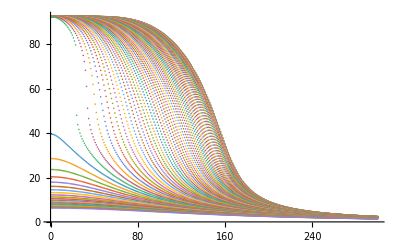

```mathematica
ListPlot[sigma0,PlotRange->All]
```

```mathematica
mu=Table[i*5.,{i,1,80}];
mu2=Table[i,{i,290,310}];
T=Table[i,{i,1,300}];
```

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,6.5,N[i],mu[[j]],300.],{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,6.5,N[i],mu2[[j]],300.],{i,1,300}],{j,1,21}];
```

```mathematica
ZdataM500=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,6.5,N[i],mu[[j]],500.],{i,1,300}],{j,1,80}];
```

```mathematica
ZdataM500p2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,6.5,N[i],mu2[[j]],500.],{i,1,300}],{j,1,21}];
```

```mathematica
(*Export["./Zdata.dat",Zdata];
Export["./Zdatap2.dat",Zdatap2];*)
```

```mathematica
(*Export["./ZdataM500.dat",ZdataM500];*)
(*Export["./ZdataM500p2.dat",ZdataM500p2];*)
```

```mathematica
(*Zdata=Import["./Zphase/Zdata.dat"];
Zdatap2=Import["./Zphase/Zdatap2.dat"];*)
```

```mathematica
(*ZdataM500=Import["./Zphase/ZdataM500.dat"];
ZdataM500p2=Import["./Zphase/ZdataM500p2.dat"];*)
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
(*ZallM500=Flatten[Table[{x=mu[[j]],y=T[[i]],ZdataM500[[j]][[i]]},{i,1,300},{j,1,58}],1];
ZallM500p2=Flatten[Table[{x=mu2[[j]],y=T[[i]],ZdataM500p2[[j]][[i]]},{i,1,300},{j,1,21}],1];
ZallM500p3=Flatten[Table[{x=mu[[j]],y=T[[i]],ZdataM500[[j]][[i]]},{i,1,300},{j,62,80}],1];*)
pb1=Import["./crossover.dat"];
pb2=Import["./firstorder.dat"];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}],ListLinePlot[pb1,PlotStyle->{Black,Dashed,Opacity[0.2]}],ListLinePlot[pb2,PlotStyle->{Black,Opacity[0.5]}]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplotM500=Rasterize[Show[ListDensityPlot[{ZallM500,ZallM500p2,ZallM500p3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1.75",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Black,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}],ListLinePlot[pb1,PlotStyle->{Black,Dashed,Opacity[0.2]}],ListLinePlot[pb2,PlotStyle->{Black,Opacity[0.5]}]],ImageResolution->300]
```

-Graphics-

```mathematica
Export["phaseM300.pdf",phaseplot];
Export["phaseM500.pdf",phaseplotM500];
```

# Produce data2

```mathematica
sigma0=Import["./sigma0.dat"];
sigma0p2=Import["./sigma0p2.dat"];
```

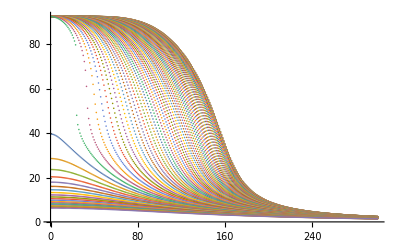

```mathematica
ListPlot[sigma0,PlotRange->All]
```

```mathematica
mu=Table[i*5.,{i,1,80}];
mu2=Table[i,{i,290,310}];
T=Table[i,{i,1,300}];
```

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,6.5,N[i],mu[[j]],300.],{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,6.5,N[i],mu2[[j]],300.],{i,1,300}],{j,1,21}];
```

```mathematica
ZdataCA=Table[ParallelTable[ZCA[(sigma0[[j]][[i]])^2/2,6.5,N[i],mu[[j]],300.],{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2CA=Table[ParallelTable[ZCA[(sigma0p2[[j]][[i]])^2/2,6.5,N[i],mu2[[j]],300.],{i,1,300}],{j,1,21}];
```

```mathematica
ZdataPH=Table[ParallelTable[ZPH[(sigma0[[j]][[i]])^2/2,6.5,N[i],mu[[j]],300.],{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2PH=Table[ParallelTable[ZPH[(sigma0p2[[j]][[i]])^2/2,6.5,N[i],mu2[[j]],300.],{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
ZallCA=Flatten[Table[{x=mu[[j]],y=T[[i]],ZdataCA[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2CA=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2CA[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3CA=Flatten[Table[{x=mu[[j]],y=T[[i]],ZdataCA[[j]][[i]]},{i,1,300},{j,62,80}],1];
ZallPH=Flatten[Table[{x=mu[[j]],y=T[[i]],ZdataPH[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2PH=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2PH[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3PH=Flatten[Table[{x=mu[[j]],y=T[[i]],ZdataPH[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{ZallCA,Zallp2CA,Zallp3CA},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

# moat boundary

```mathematica
phaseplot2=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,White},Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"]},PlotLegends->None,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangePadding->None(*,ImagePadding->None*),Epilog->{Rotate[Style[Text["Crossover",{130,150}],Bold,13],-Pi/11,{130,150}],Rotate[Style[Text["1st-order PT",{260,13}],Bold,10],0,{260,13}],Rotate[Style[Text["CEP",{275,35}],Bold,Red,10],0,{275,35}],Rotate[Style[Text["Moat",{295,255}],Bold,13],-Pi/5,{295,255}],Rotate[Style[Text["boundary",{340,200}],Bold,13],-Pi/3,{340,200}]}],ListLinePlot[pb1,PlotStyle->{Black,Dashed,Opacity[0.2]}],ListLinePlot[pb2,PlotStyle->{Black,Opacity[0.5]}],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}]],ImageResolution->600]
```

-Graphics-

```mathematica
Export["./phase.pdf",phaseplot2]
```

./phase.pdf